# One Dimensional spin chain with dipolar long range interaction - iMPS solution

## Definition of Hamiltonian

This defines the Hamiltonian matrix. I need to call Ham(λ) to get the two spin tensor.

```mathematica
Z={{1,0},{0,-1}};
X={{0,1},{1,0}};
Y={{0,-I},{I,0}};
Id={{1,0},{0,1}};
P={{0,1},{0,0}};
M={{0,0},{1,0}};
ZZ=KroneckerProduct[Z,Z];
PM=KroneckerProduct[P,M];
MP=KroneckerProduct[M,P];
ZZI=KroneckerProduct[Z,Z,Id];
ZIZ=KroneckerProduct[Z,Id,Z];
ZZII=KroneckerProduct[Z,Z,Id,Id];
ZIZI=KroneckerProduct[Z,Id,Z,Id];
ZIIZ=KroneckerProduct[Z,Id,Id,Z];
PMI=KroneckerProduct[P,M,Id];
MPI=KroneckerProduct[M,P,Id];
PIM=KroneckerProduct[P,Id,M];
MIP=KroneckerProduct[M,Id,P];
PMII=KroneckerProduct[P,M,Id,Id];
MPII=KroneckerProduct[M,P,Id,Id];
PIMI=KroneckerProduct[P,Id,M,Id];
MIPI=KroneckerProduct[M,Id,P,Id];
PIIM=KroneckerProduct[P,Id,Id,M];
MIIP=KroneckerProduct[M,Id,Id,P];
```

```mathematica
Ham[J_,n_]:=Switch[n,
2,ZZ-J(PM+MP),
3,ZZI-J(PMI+MPI)+(ZIZ-J(PIM+MIP))/2^3,
4,ZZII-J(PMII+MPII)+(ZIZI-J(PIMI+MIPI))/2^3+(ZIIZ-J(PIIM+MIIP))/3^3];
Hz[h_]:=h {{1,0},{0,-1}};
```

### Expectation Value of Energy using iMPS

```mathematica
Energy[iMPS_,J_,μ_]:=Module[{xxCorr,zzCorr,yyCorr,numTensors,z,xenergy,yenergy,zenergy},
numTensors=Length[iMPS];
xxCorr=iTEBDCorrelationList[iMPS,X,X,numTensors];
yyCorr=iTEBDCorrelationList[iMPS,Y,Y,numTensors];
zzCorr=iTEBDCorrelationList[iMPS,Z,Z,numTensors];
xenergy=(-J/2)(1/#^3&/@Range[numTensors]).xxCorr;
yenergy=(-J/2)(1/#^3&/@Range[numTensors]).yyCorr;
zenergy=-μ Expectation1O[Z,iMPS]+(1/#^3&/@Range[numTensors]).zzCorr;
Chop[xenergy+yenergy+zenergy]
]
```

{{{SparseArray[<1>,{20,20}],SparseArray[<1>,{20,20}]},SparseArray[<1>,{20}]},{{SparseArray[<1>,{20,20}],SparseArray[<1>,{20,20}]},SparseArray[<1>,{20}]},{{SparseArray[<1>,{20,20}],SparseArray[<1>,{20,20}]},SparseArray[<1>,{20}]},{{SparseArray[<1>,{20,20}],SparseArray[<1>,{20,20}]},SparseArray[<1>,{20}]}}

```mathematica
With[{num=3},
starttebd=ConstructProductiTEBD[num];
τ=0.025;
J=0.5;μ=-0.2;
Hnn=MatrixExp[-  Ham[J,num] τ/2];
Hn=MatrixExp[-Hz[μ] τ];
fullHams={Hn,Hnn};
H2=MatrixExp[-  Ham[J,2] τ/2];
H3=MatrixExp[-  (Ham[J,2]/2^3) τ/2];
H4=MatrixExp[- ( Ham[J,2]/3^3) τ/2];
swapHams=Take[{Hn,H2,H3,H4},num];
eprev=Energy[starttebd,J,μ]
]
```

0.334816

```mathematica
tebd=starttebd;
Monitor[Timing[sw=Table[EvolutionWithSwaps[swapHams,tebd];
Energy[tebd,J,μ],{ie4,1,100}]][[1]],ie4]
```

91.2898

```mathematica
tebd2=starttebd;
Monitor[Timing[fu=Table[iTEBDEvolution[fullHams,tebd2];
Energy[tebd2,J,μ],{ie4,1,100}]][[1]],ie4]
```

88.2242

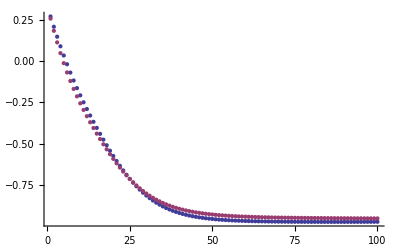

```mathematica
ListPlot[{fu,sw}]
```

```mathematica
Expectation1O[Z,tebd]
```

0.0169068

```mathematica
A0=Sqrt[3]{{0,1,0},{0,0,1},{0,0,0}};
A1=Sqrt[3]{{0,0,0},{0,0,0},{1,0,0}};
L={1,1,1}/Sqrt[3];
iMPS=N[{{{PadRight[A0,{MaxBondDimension,MaxBondDimension}],PadRight[A1,{MaxBondDimension,MaxBondDimension}]},PadRight[L,{MaxBondDimension}]},{{PadRight[A0,{MaxBondDimension,MaxBondDimension}],PadRight[A1,{MaxBondDimension,MaxBondDimension}]},PadRight[L,{MaxBondDimension}]},{{PadRight[A0,{MaxBondDimension,MaxBondDimension}],PadRight[A1,{MaxBondDimension,MaxBondDimension}]},PadRight[L,{MaxBondDimension}]}}];
```

### Test if rotate is the problem:MAYBE, but the problem appears after rotate and non-unitary evolution

```mathematica
Expectation1O[Z,iMPS]
```

0.333333

```mathematica
iTEBD3QGate[iMPS,Hnn]
```

-0.682149

```mathematica
Expectation1O[Z,iMPS]
```

0.333296

```mathematica
iMPS=RotateRight[iMPS,1];
```

```mathematica
Expectation1O[Z,iMPS]
```

0.333333